# Test for inherent g

```mathematica
plist={3.70,3.71,3.72,3.73,3.74,3.75,3.76,3.77}
```

{3.7,3.71,3.72,3.73,3.74,3.75,3.76,3.77}

```mathematica
ka1=Table[Import["/home/chengling/Research/Project/Cell/glassyDynamics/localTest/inherentg/N1024/inherentgAffineG_N1024_p3.7"<>ToString[p]<>"0_KA1.000000.4.nc","Data"],{p,0,7}];
ka001=Table[Import["/home/chengling/Research/Project/Cell/glassyDynamics/localTest/inherentg/N1024/inherentgAffineG_N1024_p3.7"<>ToString[p]<>"0_KA0.010000.4.nc","Data"],{p,0,7}];
```

```mathematica
Mean[Normal[ka1[[1,1]]]]
```

0.290506

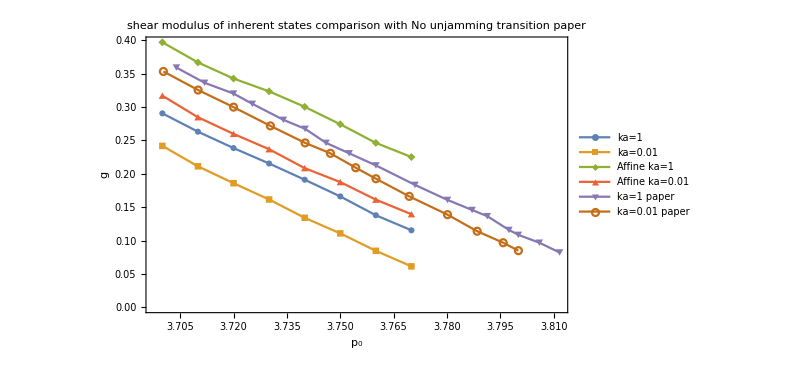

```mathematica
comparisonPlot=ListPlot[{Table[{plist[[p]],Mean[Normal[ka1[[p,1]]]]},{p,Length[plist]}],Table[{plist[[p]],Mean[Normal[ka001[[p,1]]]]},{p,Length[plist]}],Table[{plist[[p]],Mean[Normal[ka1[[p,2]]]]/1024},{p,Length[plist]}],Table[{plist[[p]],Mean[Normal[ka001[[p,2]]]]/1024},{p,Length[plist]}],ka1paper,ka001paper},PlotLegends->{"ka=1","ka=0.01","Affine ka=1","Affine ka=0.01","ka=1 paper","ka=0.01 paper"},PlotMarkers->Automatic,PlotLabel->"shear modulus of inherent states
comparison with No unjamming transition paper",ImageSize->600,PlotRange->All,Joined->True,FrameLabel->{"p_0","g"}]
```

```mathematica
Export["/home/chengling/Research/Project/Cell/glassyDynamics/plots/inherentG.jpeg",comparisonPlot,ImageResolution->400]
```

/home/chengling/Research/Project/Cell/glassyDynamics/plots/inherentG.jpeg

```mathematica
ka001paper={{3.700290275761974,0.35321790036645884},
{3.7100435413642963,0.3254284487528356},
{3.72,0.2998253348649752},
{3.7303628447024675,0.2717463384608707},
{3.7401161103047897,0.2462969732032361},
{3.7472278664731498,0.2306690483206846},
{3.7543396226415098,0.2090666197558951},
{3.7600290275761976,0.19261828373526146},
{3.769375907111756,0.16620365470595697},
{3.780145137880987,0.13878698920837695},{3.7884760522496372,0.11400909592048815},
{3.795791001451379,0.09677543331340013},
{3.8000580551523946,0.08488395818952281}};
```

```mathematica
ka1paper={{3.703947750362845,0.35905430842063735},{3.711872278664732,0.33627175576570095},
{3.72,0.3201386271998944},
{3.7252830188679247,0.30477950903745404},
{3.7340203193033386,0.2808009524285364},
{3.7401161103047897,0.26732911666101833},
{3.7460087082728593,0.2462969732032361},
{3.7525108853410742,0.2306690483206846},
{3.7600290275761976,0.21252113919598364},
{3.77100145137881,0.18337714027808946},
{3.780145137880987,0.16084430702439717},
{3.787053701015965,0.14578104787522406},
{3.791320754716981,0.13653101432481698},
{3.7974165457184323,0.11589292911520903},
{3.8000580551523946,0.1085393430476416},
{3.8059506531204645,0.09677543331340013},
{3.8116400580551524,0.08214681835147608},};
```